## Bifurcation Plots of Discrete Population Models

## Import Data

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal"];
```

```mathematica
(* Standard Ricker *)
dataRicker=Import["ricker_std/data_export/bif_data_ricker.csv"];
```

```mathematica
(* Seasonal Ricker *)
dataRickerSeasX= Import["ricker_seasonal/data_export/bif_data_x.csv"]; (* pop post breeding period *)
dataRickerSeasY= Import["ricker_seasonal/data_export/bif_data_y.csv"]; (* pop post non-breeding period *)
```

```mathematica
(* Seasonal Ricker with COE *)
dataRickerSeasCOEX=Import["ricker_seasonal_coe/data_export/bif_data_x.csv"];(* pop post breeding period *)
dataRickerSeasCOEY=Import["ricker_seasonal_coe/data_export/bif_data_y.csv"];(* pop post breeding period *)
```

```mathematica
(* Discrete logistic model *)
dataLog=Import["logistic_std/data_export/bif_data.csv"];
(* Seasonal logistic model *)
dataLogSeasX=Import["logistic_seasonal/data_export/bif_data_x.csv"];
dataLogSeasY=Import["logistic_seasonal/data_export/bif_data_y.csv"];
(* Seasonal logistic model with COE *)
dataLogSeasCOEX=Import["logistic_seasonal_coe/data_export/bif_data_x.csv"];
dataLogSeasCOEY=Import["logistic_seasonal_coe/data_export/bif_data_y.csv"];
```

```mathematica
(* Proportion of data to plot - reduce for editing - max for final product (saves comp. time) *)
prop=0.5;
```

```mathematica
(* Figure parameters *)
xRange = {1,5};
aRatio=0.5;
imgs=400;
labelPos=Scaled[{0.04,0.9}];
```

```mathematica
(* Paramters of model (from Betini et al.) *)
kb=224; (* Carrying capacity for breeding period *)
knb=-84.52;  (* Carrying capacity for non-breeding period *)
rnb=-0.0568 ; (* Growth rate for non-breeding period *)
```

## General Functions

### Function to take bifurcation data and output plotting data

```mathematica
plotData[bifData_, norm_]:=Module[{rVals,stateVals,stateValsNorm,plotVals},
(* Extract growth (r) values and state values *)
rVals=bifData[[1,2;;]];
stateVals=bifData[[2;;,2;;]];
(* Normalise state values (usually by the carrying capacity *)
stateValsNorm=stateVals/norm;
(* Plot into plotting form *)
plotVals=Table[Transpose[{rVals,stateValsNorm[[i]]}],{i,1,Length[stateVals]}]
]
```

### Function to create bifurcation diagram

```mathematica
Clear[bifPlot]
Options[bifPlot]={xaxes->False,yaxes->False,color->TMBcolours[[1]],label->"a"};
bifPlot[pData_,OptionsPattern[]]:=Module[{},
ListPlot[pData[[1;;Floor[prop*Length[pData]]]],
Frame->True,
FrameLabel->{{"Population size (N/K)",None},{"Growth rate (r_b)",None}},
FrameStyle->{{If[OptionValue[yaxes],Automatic,FontOpacity->0],Automatic},{If[OptionValue[xaxes],Automatic,FontOpacity->0],Automatic}},
PlotRange->{xRange,{0,5}},
PlotStyle->Directive[{OptionValue[color],PointSize[0.002]}],
AspectRatio->aRatio,
ImageSize->imgs,
LabelStyle->14,
Epilog->Text[Style[OptionValue[label],14,Bold],labelPos]]
]
```

## Individual Bifurcation Plots

### Standard Ricker

```mathematica
(* Plotting data *)
pData=plotData[dataRicker,kb];
```

```mathematica
(* Bifurcation plot *)
plotRicker=Show[bifPlot[pData,yaxes->True,label->"a"]];
```

### Seasonal Ricker

```mathematica
(* Plot Data *)
pDataX=plotData[dataRickerSeasX,kb];
pDataY=plotData[dataRickerSeasY,kb];
```

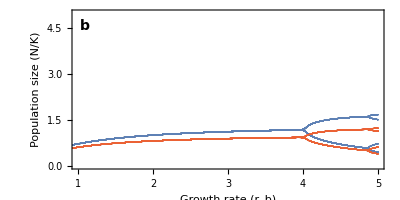

```mathematica
(* Combined bifurcation plot *)
plotRickerSeas=Show[bifPlot[pDataX,yaxes->True,label->"b"],bifPlot[pDataY,color->TMBcolours[[4]]]];
```

### Seasonal Ricker with COE

```mathematica
(* Plot Data *)
pDataX=plotData[dataRickerSeasCOEX,kb];
pDataY=plotData[dataRickerSeasCOEY,kb];
```

```mathematica
(* Combined plot *)
plotRickerSeasCOE=Show[bifPlot[pDataX,yaxes->True,xaxes->True,label->"c"],bifPlot[pDataY,color->TMBcolours[[4]]]];
```

### Discrete Logistic

```mathematica
(* Plot Data *)
pDataX=plotData[dataLog,kb];
```

```mathematica
(* Plot *)
plotLog=Show[bifPlot[pDataX,yaxes->True,label->"d"]];
```

### Discret Logistic with Seasonality

```mathematica
(* Get plotting data *)
pDataX=plotData[dataLogSeasX,kb];
pDataY=plotData[dataLogSeasY,kb];
```

```mathematica
(* Combined plot *)
plotLogSeas=Show[bifPlot[pDataX,yaxes->True,label->"e"],bifPlot[pDataY,color->TMBcolours[[4]]]];
```

### Discrete Logistic with Seasonality and COEs

```mathematica
(* Plot Data *)
pDataX=plotData[dataLogSeasCOEX,kb];
pDataY=plotData[dataLogSeasCOEY,kb];
```

```mathematica
(* Combined plot *)
plotLogSeasCOE=Show[bifPlot[pDataX,xaxes->True,yaxes->True,label->"f"],bifPlot[pDataY,color->TMBcolours[[4]]]];
```

## Combined Bifurcation Plots

```mathematica
bifPlotsRick=Grid[{{plotRicker},{plotRickerSeas},{plotRickerSeasCOE}},Spacings->{0,-0.6}];
bifPlotsLog=Grid[{{plotLog},{plotLogSeas},{plotLogSeasCOE}},Spacings->{0,-0.6}];
```

```mathematica
bifPlotComb=Grid[{{plotRicker,plotLog},{plotRickerSeas,plotLogSeas},{plotRickerSeasCOE,plotLogSeasCOE}},Spacings->{0,-0.6}];
```

```mathematica
(* Export figure at high res *)
Export["main_figures/bif_plots_ricker.png",bifPlotsRick,ImageResolution->400];
Export["main_figures/bif_plots_log.png",bifPlotsLog,ImageResolution->400];
```